Solve for the EPs

```mathematica
<<"/home/denpak/Applications/Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
alpha =5.98 - 1.07f + 31.92g
beta = 5.56-0.25f+.38g
y=alpha+beta((x-51.04)/26.98)-((x-51.04)/26.98)^3
```

5.98-1.07 f+31.92 g

5.56-0.25 f+0.38 g

5.98-1.07 f+31.92 g+0.0370645 (5.56-0.25 f+0.38 g) (-51.04+x)-0.0000509183 (-51.04+x)^3

```mathematica
y=alpha+beta x-(x)^3
```

5.98-1.07 f+31.92 g+(5.56-0.25 f+0.38 g) x-x^3

```mathematica
y//Simplify
```

5.98-1.07 f+31.92 g+(5.56-0.25 f+0.38 g) x-x^3

```mathematica
Manipulate[Plot[5.98-1.07 f+31.92 g+(5.56-0.25 f+0.38 g) x-x^3,{x,-2.0101,2.0101}],{f,1,20},{g,0,2}]
```

```mathematica
S= Solve[y==0,x]//FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→51.04-((1.67989×10^-8+2.90966×10^-8 ⅈ) (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g))/(-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)+(1.05827×10^-8-1.83297×10^-8 ⅈ) (-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)},{x→51.04-((1.67989×10^-8-2.90966×10^-8 ⅈ) (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g))/(-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)+(1.05827×10^-8+1.83297×10^-8 ⅈ) (-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)},{x→51.04+(-6.374×10^10+2.86601×10^9 f-4.35633×10^9 g)/(-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)-2.11653×10^-8 (-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)}}

```mathematica
Plot3D[{x/.S[[1]],x/.S[[2]],x/.S[[3]]},{f,0,30},{g,0,0.4}]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate[x/.S[[2]]],{f,0,30},{g,0,0.4},MaxRecursion->7,WorkingPrecision->15]
```

Plot3D::precw: The precision of the argument function (51.04-((1.67989×10^-8-2.90966×10^-8 ⅈ) («1»))/(«1»)^(1/3)+(1.05827×10^-8+1.83297×10^-8 ⅈ) (-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. Power[«2»]+Plus[«3»]^2))^(1/3)) is less than WorkingPrecision (15.).

Plot3D::precw: The precision of the argument function («1») is less than WorkingPrecision (15.).

Plot3D::precw: The precision of the argument function ({True,True,-6.19328×10^27+Re[1.10816×10^27 f-3.30585×10^28 g+√(Times[«2»]+Power[«2»])]≤0,Re[4. (-1.89714×10^18+Times[«2»]+Times[«2»])^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2]≤0}) is less than WorkingPrecision (15.).

General::stop: Further output of Plot3D::precw will be suppressed during this calculation.

```mathematica
Plot3D[{(4 -( x/.S[[2]]))/8},{f,0,20},{g,0,0.5}]
```

-Graphics3D-

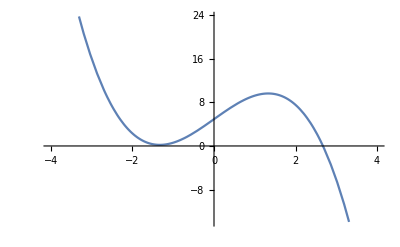
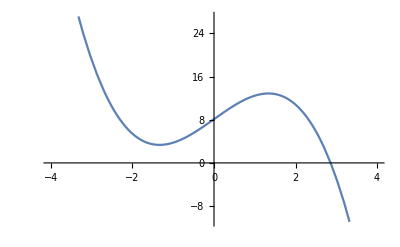
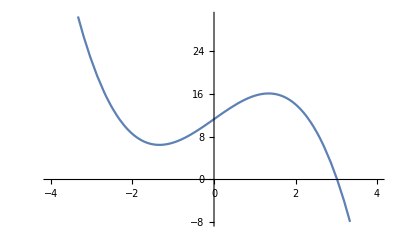
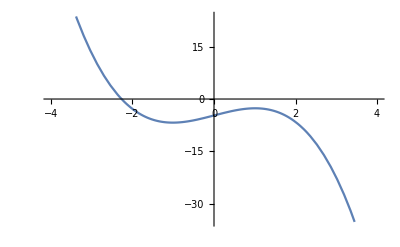
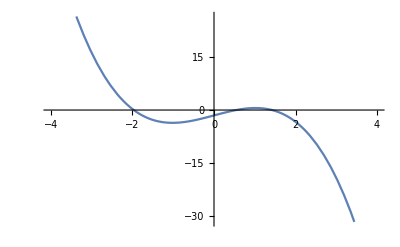
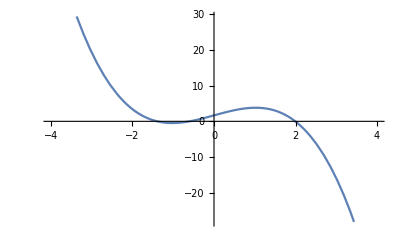
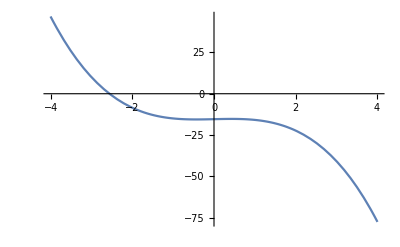
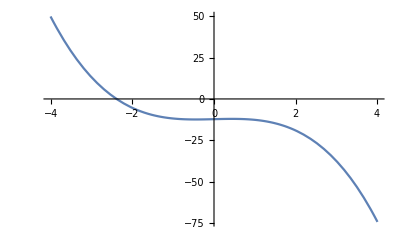

-Graphics-Arm CircumferenceArm Weight

```mathematica
plots=Table[Plot[5.98-1.07 f+31.92 g+(5.56-0.25 f+0.38 g) x-x^3,{x,-4.0101010101010102,4.0101010101010102}],{f,{1,10,20}},{g,{0,0.1,0.2}}]
imgs=Transpose@plots;
Graphics[MapIndexed[Inset[Rasterize@#,#2]&,imgs,{2}],PlotRange->Thread[{1/4,2/3+Dimensions@imgs}],Axes->True,Ticks->Range@Dimensions@imgs,AxesStyle->Arrowheads[0.03],AxesOrigin->{1/4,1/4},ImageSize->700];

Labeled[%,{"Arm Circumference","Arm Weight"},{Left,Bottom},RotateLabel->True]
```

```mathematica
.18
```

```mathematica
Manipulate[Plot[y,{x,-.01,.01}],{f,0,1},{g,0,1}]
```

```mathematica
Solve[5.98-10.7 f+31.92 g+0.037064492216456635 (5.56-0.25 f+0.38 g) (-51.04+x)-0.00005091833147753056 (-51.04+x)^3==0/.{f->2.095,g->15},x]
```

{{x→-59.5096-169.849 ⅈ},{x→-59.5096+169.849 ⅈ},{x→272.139}}

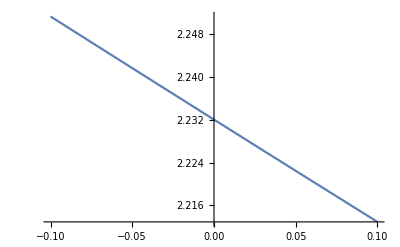
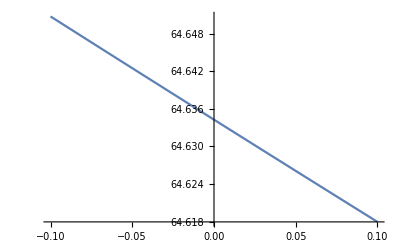
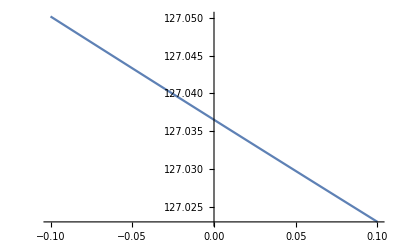
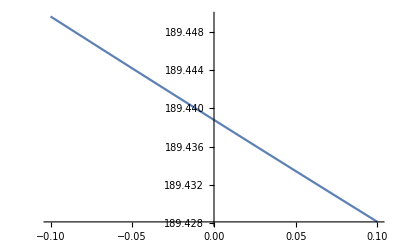
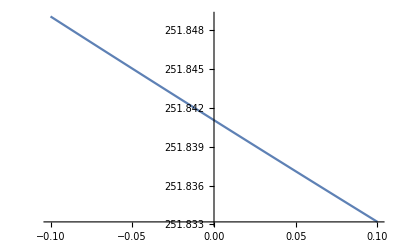
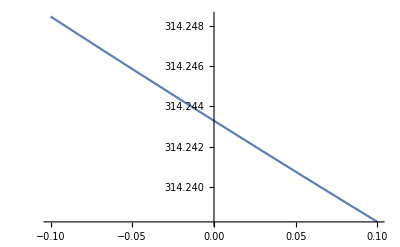
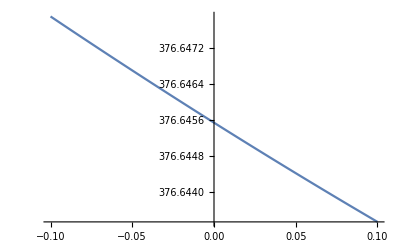
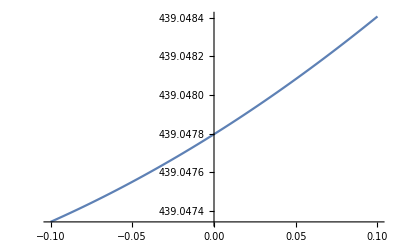
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

-Graphics-BetaAlpha

```mathematica
plots=Table[Plot[5.98-10.7 f+31.92 g+0.037064492216456635 (5.56-0.25 f+0.38 g) (-51.04+x)-0.00005091833147753056 (-51.04+x)^3,{x,-0.1,0.1}],{f,0,20,2},{g,0,20,2}]
imgs=Transpose@plots;
Graphics[MapIndexed[Inset[Rasterize@#,#2]&,imgs,{2}],PlotRange->Thread[{1/4,2/3+Dimensions@imgs}],Axes->True,Ticks->Range@Dimensions@imgs,AxesStyle->Arrowheads[0.03],AxesOrigin->{1/4,1/4},ImageSize->700];

Labeled[%,{"Beta","Alpha"},{Left,Bottom},RotateLabel->True]
```

```mathematica
""
```

```mathematica
ds = DynamicalSystem[y,{{x,-10,10}},{{f,0,100},{g,100,500}}]
alpha + beta
```

DynamicalSystem[5.98-10.7 f+31.92 g+0.0370645 (5.56-0.25 f+0.38 g) (-51.04+x)-0.0000509183 (-51.04+x)^3,{{x,-10,10}},{{f,0,100},{g,100,500}}]

11.54-10.95 f+32.3 g

Plot that branch with higher resolution

Let’s compute the central slope of this curve as a function of d

```mathematica
l2 =Plot[0.2745781780866053-1.9083893773871397 c,{c,-4,4},PlotPoints->300]
```